```mathematica
resultsDirectory="Z:\\results\\2017_11_10_expt_15_SK_dose_response";
SetDirectory[resultsDirectory]
```

1: allTracks,
2: trackToLength,
3: trackToTimeAndObjectIDAssoc,
4: timeAndObjectIDToTrackAssoc,
5: Join@@Map[processTimepointToAssociation[#]&, times], {time, channel, objectID, quantityType} -> quantity
6: pathsToImagesList

Z:\results\2017_11_10_expt_15_SK_dose_response

```mathematica
f2site1tend=Get["2018_01_10_mathematica_output_F02_0001_t20_to_tend.wl"];
f2site1t1=Get["2018_01_10_mathematica_output_F02_0001_t1_to_t19.wl"];

f6site1tend=Get["2018_01_10_mathematica_output_F06_0001_t20_to_tend.wl"];
f6site1t1=Get["2018_01_10_mathematica_output_F06_0001_t1_to_t19.wl"];

f7site1t1=Get["2018_01_10_mathematica_output_F07_0001_t1_to_t19.wl"];
f7site1tend=Get["2018_01_10_mathematica_output_F07_0001_t20_to_tend.wl"];
```

```mathematica
tracksGreaterThan20=Keys[Select[f2site1tend[[2]],#>20&]];
```

```mathematica
f2site1tend[[5]]
```

<|{1,2,1,nucSize}→109,{1,2,1,nucMeanIntensity}→41512/109,{1,2,2,nucSize}→548,{1,2,2,nucMeanIntensity}→60309/137,{1,2,3,nucSize}→933,{1,2,3,nucMeanIntensity}→727828/311,{1,2,4,nucSize}→704,{1,2,4,nucMeanIntensity}→71679/88,404665,{245,3,504,nucMeanIntensity}→13817/100,{245,3,505,nucSize}→84,{245,3,505,cytoMeanIntensity}→16476/119,{245,3,505,nucMeanIntensity}→5465/42,{245,3,506,nucSize}→168,{245,3,506,cytoMeanIntensity}→17564/75,{245,3,506,nucMeanIntensity}→12119/84|>
 |  |  |  |

```mathematica
getTrackInputs[resultsList_,channel_, quantityType_, trackID_]:=Map[{#[[1]],channel,#[[2]],quantityType}&,Normal[resultsList[[3]][trackID]]];
getTrackResults[resultsList_,channel_, quantityType_, trackID_]:=
{#[[1]],resultsList[[5]][#]}&/@getTrackInputs[resultsList,channel,quantityType,trackID];
getCytoNuclearRatio[resultsAssoc_, trackID_]:=
MapThread[{#1[[1]],N[#1[[2]]/#2[[2]]]}&,{getTrackResults[resultsAssoc,3,"cytoMeanIntensity",trackID],getTrackResults[resultsAssoc,3,"nucMeanIntensity",trackID]}];
getTrackNumbersGreaterThan[resultsAssoc_,length_]:=Keys[Select[resultsAssoc[[2]],#>length&]];
getMeanCytoNuclearRatio[resultsList_,tstart_,tend_]:=
Table[
{time,
Mean[Part[Flatten[Map[Select[#,#[[1]]==time&]&,Map[getCytoNuclearRatio[resultsList,#]&,resultsList[[1]]]],1],All,2]]},
{time,tstart,tend}];
```

```mathematica
getTrackResults[f2site1tend,2,"nucSize",4]
```

{{1,704},{2,684},{3,741},{4,743},{5,743},{6,735},{7,810},{8,729},{9,748},{10,802},{11,781},{12,816},{13,740},{14,769},{15,748},{16,769},{17,840},{18,787},{19,788},{20,826},{21,775},{22,806},{23,858},{24,898},{25,931},{26,903},{27,879},{28,883},{29,815},{30,841},{31,805},{32,856},{33,858},{34,845},{35,851},{36,881},{37,850},{38,877},{39,908},{40,905},{41,914},{42,907},{43,893},{44,909},{45,921},{46,921},{47,895},{48,889},{49,919},{50,997},{51,861},{52,937},{53,911},{54,1036},{55,999},{56,921},{57,957},{58,1013},{59,955},{60,1056},{61,999},{62,1014},{63,975},{64,971},{65,914},{66,985},{67,921},{68,826},{69,907},{70,907},{71,880},{72,926},{73,1003},{74,983},{75,1076},{76,1001},{77,1027},{78,1120},{79,1008},{80,978},{81,921},{82,821},{83,921},{84,1095},{85,152}}

```mathematica
Manipulate[
ListPlot[Map[getTrackResults[f2site1tend,2,"nucMeanIntensity",#]&,getTrackNumbersGreaterThan[f2site1tend,20][[trackNum;;trackNum+1]]],PlotStyle->Directive[Black,Thin], Joined->True,PlotRange->{{0,250},{0,3000}}],
{trackNum,Range[Length[getTrackNumbersGreaterThan[f2site1tend,20]]-5]}, ControlType->Manipulator]
```

Part::take: Cannot take positions 310 through 311 in getTrackNumbersGreaterThan[f2site1tend,20].

Part::pkspec1: The expression getTrackResults[f2site1tend,2,nucMeanIntensity,310;;311] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: getTrackResults[f2site1tend,2.,nucMeanIntensity,getTrackNumbersGreaterThan[f2site1tend,20.]]⟦getTrackResults[f2site1tend,2,nucMeanIntensity,310;;311]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification f2site1tend⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::take: Cannot take positions 310 through 311 in Keys[Part[]].

Part::partd: Part specification f2site1tend⟦3⟧ is longer than depth of object.

Part::partw: Part 2 of Keys[Part[]] does not exist.

Part::partd: Part specification f2site1tend⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression f2site1tend⟦3⟧[{310,f2site1tend⟦5⟧[{310,2,311,nucMeanIntensity}]}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],2.,Keys[Part[]]⟦2⟧,nucMeanIntensity}]}]⟦f2site1tend⟦3⟧[{310,f2site1tend⟦5⟧[{310,2,311,nucMeanIntensity}]}]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Manipulate[
ListPlot[Map[getTrackResults[f2site1tend,2,"nucSize",#]&,getTrackNumbersGreaterThan[f2site1tend,20][[trackNum;;trackNum+1]]], Joined->True,PlotRange->{{0,250},{0,3000}}],
{trackNum,Range[Length[getTrackNumbersGreaterThan[f2site1tend,20]]-5]}, ControlType->Manipulator]
```

Part::take: Cannot take positions 75 through 76 in getTrackNumbersGreaterThan[f2site1tend,20].

Part::pkspec1: The expression getTrackResults[f2site1tend,2,nucSize,75;;76] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: getTrackResults[f2site1tend,2.,nucSize,getTrackNumbersGreaterThan[f2site1tend,20.]]⟦getTrackResults[f2site1tend,2,nucSize,75;;76]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification f2site1tend⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::take: Cannot take positions 75 through 76 in Keys[Part[]].

Part::partd: Part specification f2site1tend⟦3⟧ is longer than depth of object.

Part::partw: Part 2 of Keys[Part[]] does not exist.

Part::partd: Part specification f2site1tend⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression f2site1tend⟦3⟧[{75,f2site1tend⟦5⟧[{75,2,76,nucSize}]}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],2.,Keys[Part[]]⟦2⟧,nucSize}]}]⟦f2site1tend⟦3⟧[{75,f2site1tend⟦5⟧[{75,2,76,nucSize}]}]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Manipulate[
ListPlot[Map[getTrackResults[f2site1tend,3,"cytoMeanIntensity",#]&,tracksGreaterThan20[[trackNum;;trackNum+5]]], Joined->True,PlotRange->{{0,250},{0,3000}}],
{trackNum,Range[Length[tracksGreaterThan20]]}, ControlType->Slider]
```

Part::take: Cannot take positions 1 through 6 in tracksGreaterThan20.

Part::pkspec1: The expression getTrackResults[f2site1tend,3,cytoMeanIntensity,1;;6] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: getTrackResults[f2site1tend,3.,cytoMeanIntensity,tracksGreaterThan20]⟦getTrackResults[f2site1tend,3,cytoMeanIntensity,1;;6]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 6 in tracksGreaterThan20.

Part::partd: Part specification f2site1tend⟦3⟧ is longer than depth of object.

Part::partd: Part specification tracksGreaterThan20⟦1⟧ is longer than depth of object.

Part::partd: Part specification tracksGreaterThan20⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression f2site1tend⟦3⟧[{1,f2site1tend⟦5⟧[{1,3,6,cytoMeanIntensity}]}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: f2site1tend⟦3⟧[{tracksGreaterThan20⟦1⟧,f2site1tend⟦5⟧[{tracksGreaterThan20⟦1⟧,3.,tracksGreaterThan20⟦2⟧,cytoMeanIntensity}]}]⟦f2site1tend⟦3⟧[{1,f2site1tend⟦5⟧[{1,3,6,cytoMeanIntensity}]}]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Manipulate[
ListPlot[Map[getCytoNuclearRatio[f2site1tend,#]&,getTrackNumbersGreaterThan[f2site1tend,20][[trackNum;;trackNum+5]]], Joined->True,PlotRange->{{0,250},{0,2}}],
{trackNum,Range[Length[tracksGreaterThan20]]}, ControlType->Slider]
```

Part::take: Cannot take positions 98 through 103 in getTrackNumbersGreaterThan[f2site1tend,20].

Part::pkspec1: The expression getCytoNuclearRatio[f2site1tend,98;;103] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: getCytoNuclearRatio[f2site1tend,getTrackNumbersGreaterThan[f2site1tend,20.]]⟦getCytoNuclearRatio[f2site1tend,98;;103]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification f2site1tend⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::take: Cannot take positions 98 through 103 in Keys[Part[]].

Part::partd: Part specification f2site1tend⟦3⟧ is longer than depth of object.

Part::partw: Part 2 of Keys[Part[]] does not exist.

Part::partd: Part specification f2site1tend⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of Keys[Part[]] does not exist.

MapThread::mptd: Object f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],3,Keys[Part[]]⟦2⟧,cytoMeanIntensity}]}] at position {2, 1} in MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],3,Keys[«1»]⟦2⟧,cytoMeanIntensity}]}],f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],3,Keys[«1»]⟦2⟧,nucMeanIntensity}]}]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object f2site1tend⟦3⟧[{98,f2site1tend⟦5⟧[{98,3,103,cytoMeanIntensity}]}] at position {2, 1} in MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f2site1tend⟦3⟧[{98,f2site1tend⟦5⟧[{98,3,103,cytoMeanIntensity}]}],f2site1tend⟦3⟧[{98,f2site1tend⟦5⟧[{98,3,103,nucMeanIntensity}]}]}] has only 0 of required 1 dimensions.

Part::pkspec1: The expression MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f2site1tend⟦3⟧[{98,f2site1tend⟦5⟧[{98,3,103,cytoMeanIntensity}]}],f2site1tend⟦3⟧[{98,f2site1tend⟦5⟧[{98,3,103,nucMeanIntensity}]}]}] cannot be used as a part specification.

MapThread::mptd: Object f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],3.,Keys[Part[]]⟦2⟧,cytoMeanIntensity}]}] at position {2, 1} in MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],3.,Keys[«1»]⟦2⟧,cytoMeanIntensity}]}],f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],3.,Keys[«1»]⟦2⟧,nucMeanIntensity}]}]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::pkspec1: The expression MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f2site1tend⟦3⟧[{98,f2site1tend⟦5⟧[{98,3,103,cytoMeanIntensity}]}],f2site1tend⟦3⟧[{98,f2site1tend⟦5⟧[{98,3,103,nucMeanIntensity}]}]}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 2 of #1 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: MapThread[{#1⟦1⟧,N[(Slot[«1»]⟦2⟧)/Part[«2»]]}&,{f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],3.,Part[«2»],cytoMeanIntensity}]}],f2site1tend⟦3⟧[{Part[],f2site1tend⟦5⟧[{Part[],3.,Part[«2»],nucMeanIntensity}]}]}]⟦MapThread[{#1⟦1⟧,N[(Slot[«1»]⟦2⟧)/Part[«2»]]}&,{f2site1tend⟦3⟧[{98,f2site1tend⟦5⟧[{98,3,103,cytoMeanIntensity}]}],f2site1tend⟦3⟧[{98,f2site1tend⟦5⟧[{98,3,103,nucMeanIntensity}]}]}]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Manipulate[
ListPlot[Map[getTrackResults[f6site1tend,2,"nucMeanIntensity",#]&,getTrackNumbersGreaterThan[f6site1tend,20][[trackNum;;trackNum+1]]],PlotStyle->Directive[Black,Thin], Joined->True,PlotRange->{{0,250},{0,3000}}],
{trackNum,Range[Length[getTrackNumbersGreaterThan[f6site1tend,20]]-5]}, ControlType->Manipulator]
```

Part::take: Cannot take positions 60 through 61 in getTrackNumbersGreaterThan[f6site1tend,20].

Part::pkspec1: The expression getTrackResults[f6site1tend,2,nucMeanIntensity,60;;61] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: getTrackResults[f6site1tend,2.,nucMeanIntensity,getTrackNumbersGreaterThan[f6site1tend,20.]]⟦getTrackResults[f6site1tend,2,nucMeanIntensity,60;;61]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification f6site1tend⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::take: Cannot take positions 60 through 61 in Keys[Part[]].

Part::partd: Part specification f6site1tend⟦3⟧ is longer than depth of object.

Part::partw: Part 2 of Keys[Part[]] does not exist.

Part::partd: Part specification f6site1tend⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression f6site1tend⟦3⟧[{60,f6site1tend⟦5⟧[{60,2,61,nucMeanIntensity}]}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: f6site1tend⟦3⟧[{Part[],f6site1tend⟦5⟧[{Part[],2.,Keys[Part[]]⟦2⟧,nucMeanIntensity}]}]⟦f6site1tend⟦3⟧[{60,f6site1tend⟦5⟧[{60,2,61,nucMeanIntensity}]}]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Manipulate[
ListPlot[Map[getCytoNuclearRatio[f6site1tend,#]&,getTrackNumbersGreaterThan[f6site1tend,20][[trackNum;;trackNum+5]]], Joined->True,PlotRange->{{0,250},{0,2}}],
{trackNum,Range[Length[tracksGreaterThan20]]}, ControlType->Slider]
```

Part::take: Cannot take positions 107 through 112 in getTrackNumbersGreaterThan[f6site1tend,20].

Part::pkspec1: The expression getCytoNuclearRatio[f6site1tend,107;;112] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: getCytoNuclearRatio[f6site1tend,getTrackNumbersGreaterThan[f6site1tend,20.]]⟦getCytoNuclearRatio[f6site1tend,107;;112]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification f6site1tend⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::take: Cannot take positions 107 through 112 in Keys[Part[]].

Part::partd: Part specification f6site1tend⟦3⟧ is longer than depth of object.

Part::partw: Part 2 of Keys[Part[]] does not exist.

Part::partd: Part specification f6site1tend⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of Keys[Part[]] does not exist.

MapThread::mptd: Object f6site1tend⟦3⟧[{Part[],f6site1tend⟦5⟧[{Part[],3,Keys[Part[]]⟦2⟧,cytoMeanIntensity}]}] at position {2, 1} in MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f6site1tend⟦3⟧[{Part[],f6site1tend⟦5⟧[{Part[],3,Keys[«1»]⟦2⟧,cytoMeanIntensity}]}],f6site1tend⟦3⟧[{Part[],f6site1tend⟦5⟧[{Part[],3,Keys[«1»]⟦2⟧,nucMeanIntensity}]}]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object f6site1tend⟦3⟧[{107,f6site1tend⟦5⟧[{107,3,112,cytoMeanIntensity}]}] at position {2, 1} in MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f6site1tend⟦3⟧[{107,f6site1tend⟦5⟧[{107,3,112,cytoMeanIntensity}]}],f6site1tend⟦3⟧[{107,f6site1tend⟦5⟧[{107,3,112,nucMeanIntensity}]}]}] has only 0 of required 1 dimensions.

Part::pkspec1: The expression MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f6site1tend⟦3⟧[{107,f6site1tend⟦5⟧[{107,3,112,cytoMeanIntensity}]}],f6site1tend⟦3⟧[{107,f6site1tend⟦5⟧[{107,3,112,nucMeanIntensity}]}]}] cannot be used as a part specification.

MapThread::mptd: Object f6site1tend⟦3⟧[{Part[],f6site1tend⟦5⟧[{Part[],3.,Keys[Part[]]⟦2⟧,cytoMeanIntensity}]}] at position {2, 1} in MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f6site1tend⟦3⟧[{Part[],f6site1tend⟦5⟧[{Part[],3.,Keys[«1»]⟦2⟧,cytoMeanIntensity}]}],f6site1tend⟦3⟧[{Part[],f6site1tend⟦5⟧[{Part[],3.,Keys[«1»]⟦2⟧,nucMeanIntensity}]}]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::pkspec1: The expression MapThread[{#1⟦1⟧,N[(#1⟦2⟧)/(Slot[«1»]⟦2⟧)]}&,{f6site1tend⟦3⟧[{107,f6site1tend⟦5⟧[{107,3,112,cytoMeanIntensity}]}],f6site1tend⟦3⟧[{107,f6site1tend⟦5⟧[{107,3,112,nucMeanIntensity}]}]}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: MapThread[{#1⟦1⟧,N[(Slot[«1»]⟦2⟧)/Part[«2»]]}&,{f6site1tend⟦3⟧[{Part[],f6site1tend⟦5⟧[{Part[],3.,Part[«2»],cytoMeanIntensity}]}],f6site1tend⟦3⟧[{Part[],f6site1tend⟦5⟧[{Part[],3.,Part[«2»],nucMeanIntensity}]}]}]⟦MapThread[{#1⟦1⟧,N[(Slot[«1»]⟦2⟧)/Part[«2»]]}&,{f6site1tend⟦3⟧[{107,f6site1tend⟦5⟧[{107,3,112,cytoMeanIntensity}]}],f6site1tend⟦3⟧[{107,f6site1tend⟦5⟧[{107,3,112,nucMeanIntensity}]}]}]⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

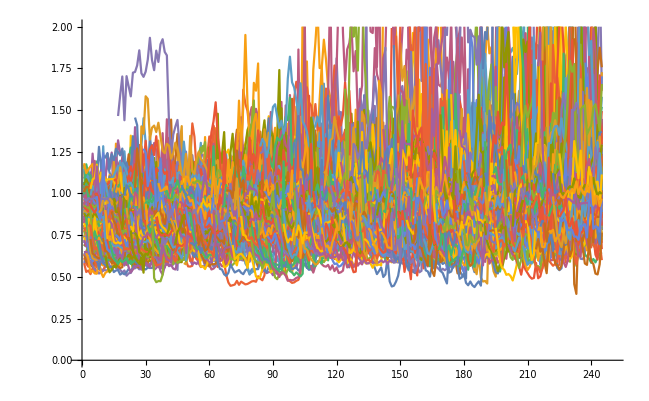

```mathematica
ListPlot[Map[getCytoNuclearRatio[f2site1tend,#]&,Keys[Select[f2site1tend[[2]],#>20&]]], Joined->True,PlotRange->{{0,250},{0,2}}]
```

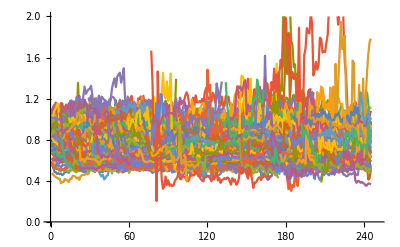

```mathematica
ListPlot[Map[getCytoNuclearRatio[f6site1tend,#]&,getTrackNumbersGreaterThan[f6site1tend,20]], Joined->True,PlotRange->{{0,250},{0,2}}]
```

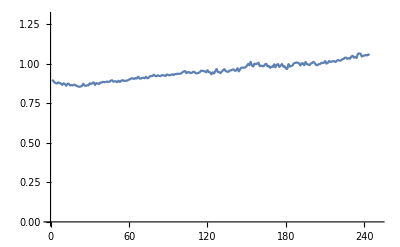

```mathematica
ListPlot[getMeanCytoNuclearRatio[f2site1tend,1,244],Joined->True,PlotRange->{{0,250},{0,1.3}}]
```

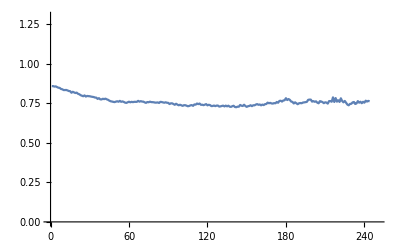

```mathematica
ListPlot[getMeanCytoNuclearRatio[f6site1tend,1,244],Joined->True,PlotRange->{{0,250},{0,1.3}}]
```

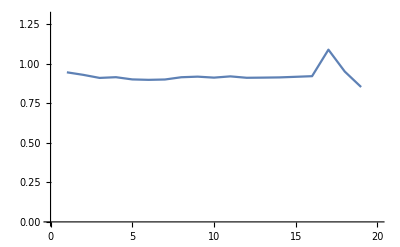

```mathematica
ListPlot[getMeanCytoNuclearRatio[f6site1t1,1,20],Joined->True,PlotRange->{{0,20},{0,1.3}}]
```

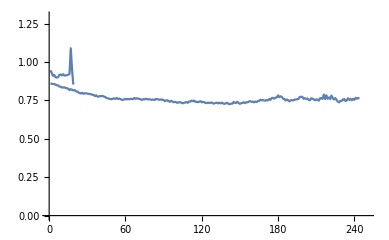

```mathematica
Show[{%147, %148}, PlotRange->{{0,250},{0,1.3}}]
```

```mathematica
getMeanCytoNuclearRatio[f6site1t1,1,20]
```

{{1,Mean[{}]},{2,Mean[{}]},{3,Mean[{}]},{4,Mean[{}]},{5,Mean[{}]},{6,Mean[{}]},{7,Mean[{}]},{8,Mean[{}]},{9,Mean[{}]},{10,Mean[{}]},{11,Mean[{}]},{12,Mean[{}]},{13,Mean[{}]},{14,Mean[{}]},{15,Mean[{}]},{16,Mean[{}]},{17,Mean[{}]},{18,Mean[{}]},{19,Mean[{}]},{20,Mean[{}]}}

```mathematica
Map[getCytoNuclearRatio[f6site1tend,#]&,getTrackNumbersGreaterThan[f6site1tend,20]]
```

{{{1,0.883687},{2,0.898981},{3,0.936903},{4,1.02389},{5,0.93916},{6,0.973736},{7,0.916514},{8,0.882972},{9,1.00391},{10,0.971405},185,{196,0.80275},{197,0.796212},{198,0.746816},{199,0.759797},{200,0.807491},{201,0.78969},{202,0.834344},{203,0.771456},{204,0.780415}},283,{1}}
 |  |  |  |

```mathematica
getMeanCytoNuclearRatio=
Table[
{time,
Mean[Part[Flatten[Map[Select[#,#[[1]]==time&]&,Map[getCytoNuclearRatio[f6site1tend,#]&,getTrackNumbersGreaterThan[f6site1tend,20]]],1],All,2]]},
{time,1,244}]
```

```mathematica
Mean[Part[Flatten[Map[Select[#,#[[1]]==2&]&,Map[getCytoNuclearRatio[f6site1tend,#]&,getTrackNumbersGreaterThan[f6site1tend,20]]],1],All,2]]
```

0.841236

```mathematica
Table[
{time,
Mean[Part[Flatten[Map[Select[#,#[[1]]==time&]&,Map[getCytoNuclearRatio[f6site1tend,#]&,getTrackNumbersGreaterThan[f6site1tend,20]]],1],All,2]]},
{time,1,244}]
```

{{1,0.840188},{2,0.841236},{3,0.839535},{4,0.839817},{5,0.836374},{6,0.833818},{7,0.833848},{8,0.829745},{9,0.828577},{10,0.822225},{11,0.821591},{12,0.825108},{13,0.820892},{14,0.820112},{15,0.820049},{16,0.812132},{17,0.812507},{18,0.815084},{19,0.811},{20,0.815423},{21,0.810829},{22,0.805513},{23,0.799375},{24,0.794876},{25,0.793161},{26,0.797369},{27,0.789557},{28,0.793184},{29,0.793635},{30,0.793241},{31,0.791655},{32,0.791277},{33,0.788795},{34,0.786208},{35,0.785155},{36,0.776913},{37,0.78176},{38,0.773285},{39,0.773442},{40,0.779109},{41,0.777246},{42,0.77991},{43,0.774258},{44,0.771215},{45,0.76545},{46,0.760865},{47,0.759353},{48,0.757766},{49,0.756562},{50,0.761697},{51,0.762602},{52,0.758538},{53,0.765539},{54,0.759678},{55,0.763023},{56,0.759821},{57,0.755206},{58,0.753155},{59,0.757435},{60,0.760956},{61,0.756301},{62,0.759613},{63,0.75746},{64,0.759473},{65,0.758112},{66,0.758251},{67,0.764294},{68,0.760191},{69,0.764103},{70,0.760824},{71,0.759793},{72,0.755443},{73,0.752835},{74,0.757788},{75,0.757444},{76,0.760267},{77,0.757448},{78,0.757226},{79,0.755986},{80,0.75395},{81,0.754117},{82,0.755127},{83,0.751905},{84,0.758602},{85,0.757559},{86,0.754131},{87,0.751369},{88,0.752044},{89,0.749787},{90,0.749085},{91,0.741402},{92,0.745623},{93,0.74352},{94,0.740039},{95,0.735917},{96,0.741365},{97,0.73661},{98,0.732926},{99,0.736787},{100,0.734314},{101,0.731811},{102,0.735639},{103,0.73734},{104,0.734249},{105,0.732224},{106,0.732106},{107,0.736245},{108,0.737569},{109,0.733096},{110,0.741878},{111,0.740754},{112,0.747993},{113,0.741677},{114,0.746345},{115,0.740707},{116,0.741557},{117,0.738714},{118,0.7418},{119,0.745245},{120,0.737524},{121,0.74108},{122,0.738871},{123,0.732829},{124,0.733527},{125,0.736224},{126,0.732619},{127,0.735885},{128,0.73607},{129,0.729607},{130,0.731197},{131,0.733617},{132,0.734225},{133,0.729537},{134,0.734596},{135,0.730096},{136,0.73416},{137,0.727923},{138,0.726694},{139,0.730628},{140,0.733273},{141,0.725628},{142,0.724104},{143,0.727634},{144,0.727709},{145,0.738676},{146,0.734292},{147,0.732692},{148,0.740715},{149,0.732944},{150,0.727581},{151,0.731559},{152,0.733779},{153,0.738135},{154,0.732495},{155,0.738017},{156,0.737702},{157,0.742411},{158,0.745407},{159,0.740884},{160,0.741803},{161,0.736342},{162,0.741121},{163,0.738561},{164,0.744058},{165,0.744702},{166,0.753255},{167,0.74763},{168,0.748633},{169,0.745988},{170,0.743211},{171,0.746517},{172,0.7479},{173,0.755599},{174,0.75006},{175,0.762488},{176,0.763768},{177,0.758427},{178,0.764948},{179,0.767134},{180,0.777753},{181,0.771665},{182,0.777356},{183,0.772044},{184,0.761458},{185,0.760065},{186,0.750186},{187,0.754675},{188,0.748479},{189,0.742917},{190,0.749648},{191,0.750503},{192,0.746594},{193,0.751342},{194,0.752813},{195,0.751204},{196,0.753479},{197,0.766994},{198,0.765573},{199,0.765988},{200,0.755409},{201,0.759924},{202,0.755464},{203,0.758158},{204,0.750851},{205,0.747251},{206,0.759628},{207,0.758593},{208,0.754314},{209,0.747233},{210,0.752844},{211,0.752808},{212,0.745345},{213,0.761867},{214,0.757464},{215,0.752774},{216,0.781033},{217,0.751651},{218,0.777449},{219,0.754014},{220,0.763257},{221,0.753575},{222,0.775305},{223,0.761402},{224,0.753008},{225,0.76139},{226,0.748296},{227,0.738152},{228,0.733393},{229,0.743505},{230,0.743665},{231,0.754148},{232,0.757592},{233,0.74353},{234,0.751147},{235,0.758157},{236,0.747658},{237,0.751297},{238,0.737196},{239,0.744509},{240,0.738195},{241,0.749875},{242,0.746891},{243,0.752391},{244,0.745652}}